```mathematica
Print["Hello world"]
```

## Define parameter values (instead of importing)

```mathematica
ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];Off[General::"spelll"];
```

ClearAll::wrsym: Symbol T is Protected.

Linkage lengths (SI units)

```mathematica
L1=5.26 *10^-3;
L2=3.18 *10^-3;
L3=0.81 *10^-3;
L4=5.11 *10^-3;
EXLocal = 1.43 *10^-3 ;
EYLocal = 1.64 *10^-3 ;
FXLocal = 5.52 *10^-3 ;
FYLocal = 4.3 *10^-3;
```

Dactyl/propdus mass

```mathematica
dMass = 4.53 *10^-4;
```

Dactyl/propdus moment of inertia

```mathematica
dI= 8.16 *10^-8 ; (* (kg m^2) *)
```

Spring at the mV joint (linear spring stiffness (N/m) * L2^2 (approx. distance to force application)

```mathematica
kSpring = (60*10^3) (3.18 *10^-3)^2;    (* Torsion spring stiffness (Nm/rad) *)
```

Max torque estimated as max force (29 N in Zack et al paper), times L2 (3.18e-3, approximate distance to force application)

```mathematica
Tmax = 29  (3.18 *10^-3);(* Max torque generated by torsion spring *)
```

Duration of simulation (s)

```mathematica
simDuration = 5 *10^-3;
```

Initial input angle, θin, at the mV joint

```mathematica
theta = (66/180) N[π];
```

## Import parameter values (instead of defining)

### Set parameters

```mathematica
KillMech[];ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];
```

ClearMech::shdw: Symbol "ClearMech" appears in multiple contexts {"MechanicalSystems`Modeler2D`", "Global`"}; definitions in context "MechanicalSystems`Modeler2D`" may shadow or be shadowed by other definitions.

```mathematica
currPath = Import["/Volumes/Docs/Projects/Patek_project/pod_model/sims/curr_path.txt",{"Text","Lines"}];
```

```mathematica
inParams = Import[StringJoin[currPath, "/input_params.mat"]][[1]];
```

```mathematica
tEval = Import[StringJoin[currPath, "/eval_time.mat"]][[1]];
```

```mathematica
L1 = inParams[[1]];
L2=inParams[[2]];
L3=inParams[[3]];
L4=inParams[[4]];
EXLocal = inParams[[5]];
EYLocal=inParams[[6]];
FXLocal=inParams[[7]];
FYLocal=inParams[[8]];
theta=inParams[[9]];
dMass=inParams[[10]];
dI=inParams[[11]];
kSpring=inParams[[12]];
Tmax=inParams[[13]];
simDuration=inParams[[14]];
```

```mathematica
Clear[inParams]
```

## Linkage model

### Rescale input parameter values

Scale Factors (Mutliplers of all parameters -- helps with numerical instabilities)

```mathematica
sL = 1 / L1;
sM = 1/dMass;
sT=10^3;
```

Apply scale factors to parameter values

```mathematica
dMass = dMass sM;
dI= dI sM sL^2;
L1=L1 sL;
L2=L2 sL;
L3=L3 sL;
L4=L4  sL;
kSpring = kSpring (sM sL^2/sT^2);
Tmax= Tmax(sM sL^2/sT^2);
EXLocal = EXLocal sL;
EYLocal = EYLocal sL;
FXLocal = FXLocal sL;
FYLocal  = FYLocal sL;
simDuration = simDuration sT;
tEval = tEval*sT;
```

### Calculated parameter values, define model inputs

Angle, ψ, btwn L1 & L4:

```mathematica
si[theta_]:=ArcCos[(h[theta]^2+L1^2-L2^2)/(2 h[theta] L1)]+ArcCos[(h[theta]^2+L4^2-L3^2)/(2 h[theta] L4)];
h[theta_]:=√(L1^2+L2^2-2 L1 L2 Cos[theta]);
```

Check that the geometry is possible (both should be 'True')

```mathematica
L4  < ( L3 + h[theta])
```

True

```mathematica
L4  > (  h[theta]-L3)
```

True

Points on the appendage

```mathematica
AX=0;
AY= 0;
BX=L2 Sin[theta];
BY=L2 Cos[theta];
CX=L4 Sin[si[theta]];
CY=L1-L4 Cos[si[theta]];
DX=0;
DY=L1;
EX =BX+ EXLocal;
EY=BY - EYLocal;
FX=BX- FXLocal;
FY=EY-FYLocal;
```

```mathematica
Clear[si,h]
```

Body addresses

```mathematica
ground = 1; mV = 2;carpus = 3;dactyl = 4;
```

Display initial geometry

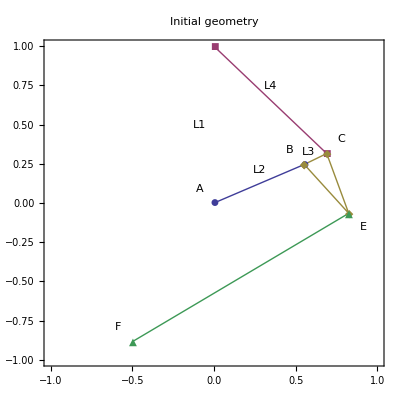

```mathematica
offset = .09 L1;
Show[
ListPlot[{
{{AX,AY},{BX,BY}},
{{CX,CY},{DX,DY}},
{{BX,BY},{EX,EY},{CX,CY},{BX,BY}},
{{EX,EY},{FX,FY}}
},
PlotMarkers->Automatic,Joined->True,
Frame->True,AspectRatio->Automatic,
PlotLabel->"Initial geometry",
PlotRange->{{-1,1},{-1,1}}],
Graphics[
{Text["A",{AX-offset,AY+offset}],Text["B",{BX-offset,BY+offset}],
Text["C",{CX+offset,CY+offset}],Text["D",{DX-offset,DY+offset}],
Text["E",{EX+offset,EY-offset}],Text["F",{FX-offset,FY+offset}],
Text["L1",{Mean[{AX,DX}]-offset,Mean[{AY,DY}]}],
Text["L2",{Mean[{AX,BX}]-offset,Mean[{AY,BY}]}+offset],
Text["L3",{Mean[{CX,BX}]-offset,Mean[{CY,BY}]}+offset/2],
Text["L4",{Mean[{DX,CX}]-offset,Mean[{DY,CY}]}+offset]
}]
]
```

### Define Bodies

```mathematica
bd[ground] = Body[ground,
PointList->{
(*P1*){DX,DY}},
InitialGuess->{
{0,0},0}
];
```

```mathematica
bd[mV] = Body[mV,
PointList->{
(*P1*){BX,BY}},
InitialGuess->{
{0,0},0}
];
```

```mathematica
bd[carpus] = Body[carpus,
   PointList -> {
     (*P1*){ CX - BX, CY - BY},
     (*P2*){ EX - BX, EY - BY}},
         InitialGuess -> {
               {BX, BY}, 0}
         ];
```

```mathematica
bd[dactyl] = Body[dactyl,
      PointList -> {
          (*P1*){FX - EX, FX - EX}},
Mass ->dMass,
Inertia ->dI,
      InitialGuess -> {
         {EX, EY}, 0}
      ];
```

```mathematica
SetBodies[bd[ground],bd[mV],bd[carpus],bd[dactyl]];
```

### Define constraints

Pin joint between ground and mV:

```mathematica
cs[1]= Revolute2[1,Point[ground,0],Point[mV,0]];
```

Initially fix position of joint at mV origin (removed later):

```mathematica
cs[2] = RotationLock1[2,  mV,0];
```

Pin joint between carpus and mV:

```mathematica
cs[3] = Revolute2[3, Point[carpus, 0], Point[mV, 1]];
```

Fix distance between ground and top of carpus:

```mathematica
cs[4] = RelativeDistance1[4, Point[carpus, 1], Point[ground, 1], L4];
```

Pin btwn carpus and dactyl

```mathematica
cs[5] = Revolute2[5, Point[dactyl, 0], Point[carpus, 2]];
```

Lock rotation btwn carpus & dactyl

```mathematica
cs[6] = RotationLock1[6, carpus, dactyl, 0];
```

```mathematica
SetConstraints[cs[1], cs[2], cs[3], cs[4],cs[5],cs[6]];
```

```mathematica
Print["Check system after constraints:" Evaluate[CheckSystem[]]]
```

Check system after constraints: True

### Evaluate kinematic model

SetParameters[{
   (*Torsion spring stiffness*)  theta -> θ
   }];

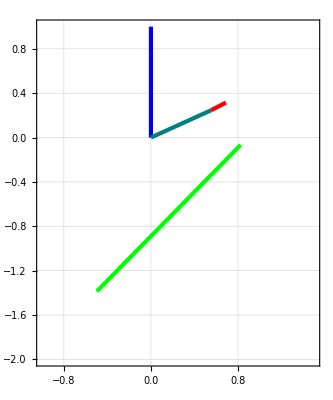

```mathematica
graph=Graphics[{
(*ground*){RGBColor[0,0,1],Bar[Axis[ground,0,1],10^-4 sL,10^-4 sL]},
(*mV*){RGBColor[0,.5,.5],Bar[Line[mV,0,1],10^-4 sL,10^-4 sL]},
(*carpus*){RGBColor[1,0,0],Bar[Line[carpus,0,1],10^-4 sL,10^-4 sL]},
(*dactyl*){RGBColor[0,1,0],Bar[Line[dactyl,0,1],10^-4 sL,10^-4 sL]}
},
Frame->True,
AspectRatio->Automatic,
GridLines->Automatic,
PlotRange->{{-1,1.5},{-2,1}}
];

Show[graph/.SolveMech[]]
```

```mathematica
Evaluate[{Angle[mV,1]}/.SolveMech[]] (180/π)
```

{24.}

### Define Loads

Moment created by the spring

```mathematica
ld[1]=Moment[mV,-(Tmax-kSpring  Θ2)];
```

Drag on dactyl

```mathematica
ld[2] = Force[dactyl, Axis[Point[dactyl, 1], -Velocity[dactyl,1]^2],5.0,Magnitude->Relative];
```

TODO: Add Acceleration reaction on dactyl

```mathematica
SetLoads[ld[1],ld[2]]
```

```mathematica
Print["Check system after loads:" Evaluate[CheckSystem[]]]
```

Check system after loads: True

### Find solution

Solution with the 4-bar linkage constrained from moving:

Remove constraint 2 (fixed angle of the mV)  & define initial conditions

```mathematica
fsys = SetFree[2,{Solution->Dynamic,
InitialCondition->{T->0,Θ2d->0,Θ3d->0,Θ4d->0,X2d->0,Y2d->0,X3d->0,Y3d->0,X4d->0,Y4d->0}}];
```

SolveFree[fsys]

```mathematica
sol=SolveFree[fsys,simDuration,MakeRules->{Location,Velocity,Acceleration}]
```

{X2→0,Y2→0,Θ2→InterpolatingFunction[{{0.,10.}},<>][T],X3→InterpolatingFunction[{{0.,10.}},<>][T],Y3→InterpolatingFunction[{{0.,10.}},<>][T],Θ3→InterpolatingFunction[{{0.,10.}},<>][T],X4→InterpolatingFunction[{{0.,10.}},<>][T],Y4→InterpolatingFunction[{{0.,10.}},<>][T],Θ4→InterpolatingFunction[{{0.,10.}},<>][T],X2d→0,Y2d→0,Θ2d→InterpolatingFunction[{{0.,10.}},<>][T],X3d→InterpolatingFunction[{{0.,10.}},<>][T],Y3d→InterpolatingFunction[{{0.,10.}},<>][T],Θ3d→InterpolatingFunction[{{0.,10.}},<>][T],X4d→InterpolatingFunction[{{0.,10.}},<>][T],Y4d→InterpolatingFunction[{{0.,10.}},<>][T],Θ4d→InterpolatingFunction[{{0.,10.}},<>][T],X2dd→0.,Y2dd→0.,Θ2dd→InterpolatingFunction[{{0.,10.}},<>][T],X3dd→InterpolatingFunction[{{0.,10.}},<>][T],Y3dd→InterpolatingFunction[{{0.,10.}},<>][T],Θ3dd→InterpolatingFunction[{{0.,10.}},<>][T],X4dd→InterpolatingFunction[{{0.,10.}},<>][T],Y4dd→InterpolatingFunction[{{0.,10.}},<>][T],Θ4dd→InterpolatingFunction[{{0.,10.}},<>][T]}

### Simulation diagnostics (for debugging)

```mathematica
Constraints[1]/.sol
Constraints[3]/.sol
Constraints[4]/.sol
```

{0,0}

{-0.552296 Cos[InterpolatingFunction[{{0.,10.}},<>][T]]+0.245898 Sin[InterpolatingFunction[{{0.,10.}},<>][T]]+InterpolatingFunction[{{0.,10.}},<>][T],-0.245898 Cos[InterpolatingFunction[{{0.,10.}},<>][T]]-0.552296 Sin[InterpolatingFunction[{{0.,10.}},<>][T]]+InterpolatingFunction[{{0.,10.}},<>][T]}

{-0.943779+(-1.+0.0697922 Cos[InterpolatingFunction[{{0.,10.}},<>][T]]+0.137269 Sin[InterpolatingFunction[{{0.,10.}},<>][T]]+InterpolatingFunction[{{0.,10.}},<>][T])^2+(0.137269 Cos[InterpolatingFunction[{{0.,10.}},<>][T]]-0.0697922 Sin[InterpolatingFunction[{{0.,10.}},<>][T]]+InterpolatingFunction[{{0.,10.}},<>][T])^2}

```mathematica
StepMech[]
```

{X2→0.,Y2→0.,Θ2→0.,X3→0.552296,Y3→0.245898,Θ3→0.,X4→0.824159,Y4→-0.0658893,Θ4→0.}

```mathematica
Loads[{mV,carpus}]
```

{0,0,-7.35793+48.4101 Θ2,0,0,0}

### Draw bodies

```mathematica
graph = Graphics[{
{RGBColor[0, 0, 1], Bar[Line[ground, 0, 1], sL/10^4, sL/10^4]}, 
{RGBColor[0, 0.5, 0.5], Bar[Line[mV, 0, 1], sL/10^4, sL/10^4]}, 
{RGBColor[1, 0, 0], Bar[Line[carpus, 0, 1], sL/10^4, sL/10^4]}, 
{RGBColor[0, 1, 0], Bar[Line[dactyl, 0, 1], sL/10^4, sL/10^4]}}, 
Frame -> True, AspectRatio -> Automatic, GridLines -> Automatic];
```

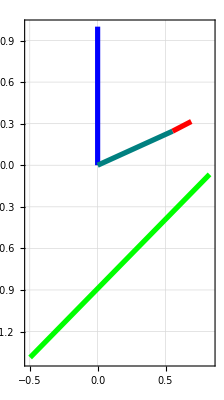

```mathematica
Show[graph/.(sol/.{T->0*simDuration})]
```

numPlot = 10; GraphicsGrid[{graph /. (sol /. Table[{T -> i}, {i, 0, simDuration, simDuration/numPlot}] )}]

Animate[Show[graph /. (sol /. {T -> i})], {i, 0, simDuration, .1}]

### Graph results

Theta (angle btwn mV and ground (L1))

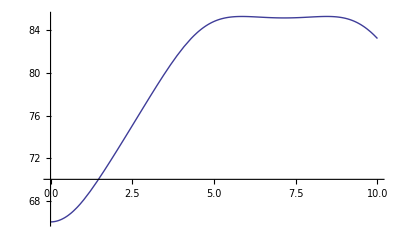

```mathematica
Plot[Evaluate[{Angle[ground,1]-Angle[mV,1]}/.sol] (180/π),{T,0,simDuration}]
```

Angle of mV in global frame of reference

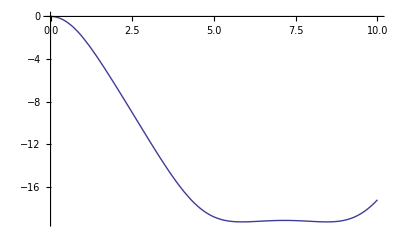

```mathematica
Plot[Evaluate[{ Θ2}/.sol] (180/π),{T,0,simDuration}]
```

Distance between point on dactyl and origin

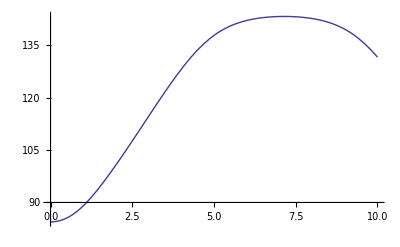

```mathematica
Plot[Evaluate[{Distance[Point[dactyl,1],{0,0}]}/.sol] (180/π),{T,0,simDuration}]
```

### Export data

```mathematica
(* P1 on carpus *)
carp1Kine=
{((Location[Point[carpus,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[carpus,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/carpusP1.mat"],carp1Kine,"MAT"];
```

```mathematica
(* P2 on carpus *)
carp2Kine=
{((Location[Point[carpus,2]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[carpus,2]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/carpusP2.mat"],carp2Kine,"MAT"];
```

```mathematica
(* P1 on ground *)
gnd1Kine=
{((Location[Point[ground,2]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[ground,2]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[ground,2]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[ground,2]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[ground,2]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[ground,2]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/groundP1.mat"],gnd1Kine,"MAT"];
```

```mathematica
(* P1 on mV *)
mV1Kine=
{((Location[Point[mV,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[mV,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[mV,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[mV,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[mV,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[mV,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/mVP1.mat"],mV1Kine,"MAT"];
```

```mathematica
(* P1 on dactyl *)
dac1Kine=
{((Location[Point[dactyl,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[dactyl,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/dactylP1.mat"],dac1Kine,"MAT"];
```